```mathematica
(* Exercício Programa 4 - Cálculo Numérico - Pedro Trama Fernandes Pereira - RA: 254344  *)
```

```mathematica
(*Definindo a função dada:*)
f[x_]:=1/(1+Exp[(x-5)/0.5])
(*Plotando a função dada:*)
```

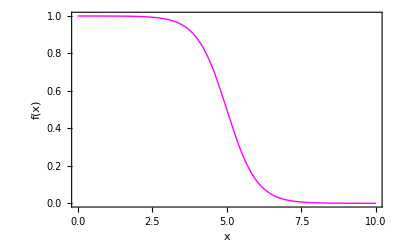

```mathematica
Plot[f[x],{x,0,10},Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{"x","f(x)"},PlotStyle->{Magenta, Thick}]
```

```mathematica
(*Definindo o intervalo da função*)
xi=0.0; xf=10.0;Np=101; 
Δx = (xf - xi)/(Np-1);
x=Table[i,{i,xi,xf,Δx}] ;
(*Definindo a equação da derivada primeira*)
```

```mathematica
xdfdxC=Table[{x[[i]],(f[x[[i+1]]]-f[x[[i-1]]])/(2 Δx)},{i,2,Np-1}] ;
(*Plotando o gráfico*)
```

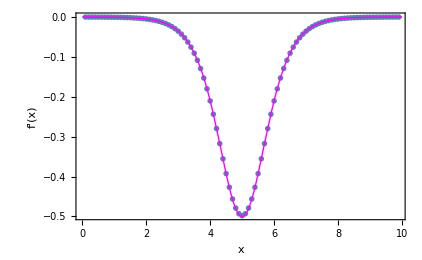

```mathematica
Show[
ListPlot[{xdfdxC},PlotMarkers->{{Green,Small}},Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{"x","f'(x)"}],
 Plot[f'[x],{x,0,10},Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{"x","f'(x)"},PlotStyle->{Magenta,Thick}]
]
```

```mathematica
(*Definindo a equação da derivada segunda*)
```

```mathematica
xd2fdx2C=Table[{xdfdxC[[i,1]],(xdfdxC[[i+1,2]]-xdfdxC[[i-1,2]])/(2 Δx)},{i,2,Np-3}] ;
```

```mathematica
(*Plotando o gráfico*)
```

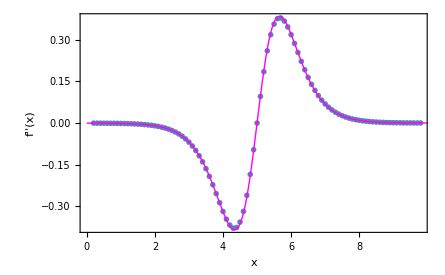

```mathematica
Show[
ListPlot[{xd2fdx2C},PlotMarkers->{{Green,Small}},Frame->True,FrameStyle->Directive[Black,20],FrameLabel->{"x","f''(x)"}],
Plot[f''[x],{x,0,10},Frame->True,FrameStyle->Directive[Black,25],FrameLabel->{"x","f''(x)"},PlotStyle->{Magenta,Thick}]
]
```